### Definitions

```mathematica
dir["datasets"]=FileNameJoin[{NotebookDirectory[],"datasets"}];
dir["plots"]=FileNameJoin[{NotebookDirectory[],"plots"}];
mesonsP={"π^0","η","η'"};
{mapMeson["π^0"],mapMeson["η"],mapMeson["η'"],mapMeson["ρ^0"],mapMeson["ϕ"]}={"Pi0","Eta","EtaPr","Rho0","Phi"};
mπval=mP["π^0"]=MASS["π^0"]=0.135;
mηval=mP["η"]=MASS["η"]=0.547;
mP["π^+"]=mP["π^-"]=MASS["π^+"]=MASS["π^-"]=0.13957;
MASS["K^+"]=MASS["K^-"]=0.493677;
MASS["K_L"]=MASS["K_S"]=0.497611;
mηprval=mP["η'"]=MASS["η'"]=0.958;
fatest=0.093;
setups={"Baseline","Baseline-FBD-upgrade","Optimal","High-energy"};
```

### Stylings

```mathematica
ticksx={{0.05,"0.05",0.01},{0.1,"0.1",0.015},{0.2,"0.2",0.01},{0.5,"0.5",0.01},{1,"1",0.015},{2,"2",0.01}};
ticksxRight=SortBy[Join[Table[{10.^j,"",0.011},{j,-20,5,1}]],#[[1]]&];
ticksy=SortBy[Join[Table[{10.^j,If[OddQ[j],Superscript["10",ToString[j//IntegerPart]],""],0.011},{j,-20,20,1}]],#[[1]]&];
ticksyRight=SortBy[Table[{10.^j,"",0.011},{j,-20,20,1}],#[[1]]&];
ticks={{ticksy,None},{ticksx,None}};
```

### Plots

#### Fig. 2

Importing

```mathematica
Do[
MesonsNumbers[setup]=Import[FileNameJoin[{dir["datasets"],"mesons-production-"<>setup<>".mx"}],"MX"];
ALPnumbers[setup]=Import[FileNameJoin[{dir["datasets"],"ALP-production-cross-section-"<>setup<>".mx"}],"MX"];
,{setup,setups}];
setups=Keys[DownValues@MesonsNumbers][[All,1,1]];
Do[
Do[
With[{mes=MesonsNumbers[set][[i,1]]},{σTotMeson[mes,set],σCutsMeson[mes,set]}=MesonsNumbers[set][[i,#]]&/@{2,3}]
,{i,1,Length[MesonsNumbers[set]]}]
,{set,setups}]
mesonsList=MesonsNumbers[setups[[1]]][[All,1]];
Plist=Select[mesonsList,MemberQ[{"π^0","η","η'"},#]&];
data={};
Do[
(*plTot={{mP[#],σTotP[#,set]}}&/@Plist;*)
plCut[set]={MASS[#],btofb*σCutsMeson[#,set]}&/@Plist;
,{set,setups}]
data=Flatten[Table[Table[plCut[set][[i]],{i,1,Length[Plist],1}],{set,setups}]//Transpose,1];
```

Styling

```mathematica
labels={Style["mass [GeV]",FontSize->22,FontFamily->"Palatino"],Style["σ [fb]",FontSize->22,FontFamily->"Palatino"]}
moddef=Style["E_p = 275 GeV",FontSize->20,FontFamily->"Palatino"];
```

{mass [GeV],σ [fb]}

Plots

```mathematica
Plist
```

{π^0,η,η'}

0.05

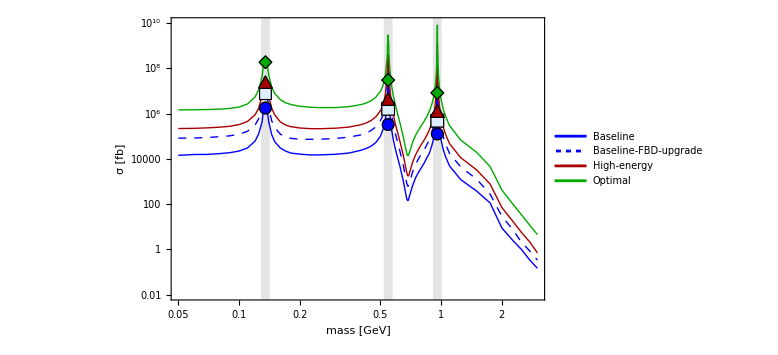

/Users/maksymovchynnikov/Library/CloudStorage/Dropbox/Science 2/HNL and scalar phenomenology/ALPs at EIC/release/plots/sigma-total.pdf

```mathematica
masses=MASS[#]&/@Plist;
dx=0.05
pt1=ListLogLogPlot[Evaluate[Table[{#[[1]],#[[3]]*btofb}&/@ALPnumbers[set],{set,setups}]],Joined->True,Frame->True,ImageSize->Large,PlotRange->{{0.05,3},btofb{10^-17,10^-5}},FrameLabel->labels,PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.01]},{Thick,Darker@Red},{Thick,Darker@Green}},FrameStyle->Directive[FontFamily->"Palatino",Thick,Black,22],FrameTicks->ticks,PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@setups,{0.28,0.22}],Prolog->{{GrayLevel[0.85],Opacity[0.7],EdgeForm[None],Rectangle[{#-dx,Log[0.0001]},{#+dx,Log[10^14]}]&/@Log[masses]}}];
(*tri=Graphics[Polygon[{{0,0},{1,0},{0.5,0.9}}]];*)
tr[color_]:=Graphics[{EdgeForm[Black],FaceForm[color],Polygon[{{0,0},{1,0},{0.5,0.9}}]}];
sq[color_]:=Graphics[{EdgeForm[Black],FaceForm[color],Rectangle[]}];
circ[color_]:=Graphics[{EdgeForm[Black],FaceForm[color],Disk[]}];
diam[color_]:=Graphics[{EdgeForm[Black],FaceForm[color],Polygon[{{0.5,0},{1,0.5},{0.5,1},{0,0.5}}]}];
ep=Graphics[{Inset[Framed[Style[Row[{moddef}],FontSize->16,FontColor->Black],FrameStyle->Directive[Black,Opacity[0.8]],Background->Directive[White,Opacity[0.9]],RoundingRadius->.01],Scaled[{0.85,0.1}],Center]}];
pt2=ListLogLogPlot[Partition[data,1],(* <--pass two series*)PlotMarkers->{{circ[Blue],12},{sq[LightBlue],12},{tr[Darker@Red],14},{diam[Darker@Green],13},{circ[Blue],12},{sq[LightBlue],13},{tr[Darker@Red],14},{diam[Darker@Green],13},{circ[Blue],12},{sq[LightBlue],13},{tr[Darker@Red],14},{diam[Darker@Green],13}},(*one marker per series*)PlotStyle->({Thick,#}&/@{Blue,LightBlue,Darker@Red,Darker@Green,Blue,LightBlue,Darker@Red,Darker@Green,Blue,LightBlue,Darker@Red,Darker@Green}),Frame->True,PlotRange->All,ImageSize->Large];
pt3=Show[pt1,pt2]
Export[FileNameJoin[{dir["plots"],"sigma-total.pdf"}],pt3]
```

## Kinematics correlation

### Data importing/generating

```mathematica
(*If generating total cross-section - MC*)
ifGenerateσ=False;
fileσ=FileNameJoin[{dir["datasets"],"MC calculation","cross-sections-mesons-setups.mx"}];
If[!FileExistsQ[fileσ],ifGenerateσ=True];
(*If generating analytic dσ/dQ^2*)
ifGeneratedσdQ2ini=False;
{σ2to3Total,mesonSample,dσdQ22to3analytic}//Clear;
Block[{EnergiesConfigurations={"100×10","275×18","41×5"},allMesons=Join[mesonsP,mesonsV],NeventsTest=5*10^6,Ep,Ee},
Print["Generating/importing total cross-section..."];
If[ifGenerateσ,
ResourceFunction["MonitorProgress"]@Do[
{Ep,Ee}=energies[setup];
Print[Row[{"Setup ", setup}]];
ResourceFunction["MonitorProgress"]@Do[
BlockFinal[P,MASS[P],fatest,Ep,Ee,NeventsTest,MASS[P],mpval,Ep,0.,-3.,14.,0.,2.];
σ2to3Total[setup,P]=σtot;
,{P,allMesons}];
,{setup,EnergiesConfigurations}];
tabMesonsAll=Flatten[Table[{setup,P,σ2to3Total[setup,P]},{setup,EnergiesConfigurations},{P,allMesons}],1];
Export[fileσ,tabMesonsAll,"MX"]
,
tabMesonsAll=Import[fileσ,"MX"];
Do[
σ2to3Total[tabMesonsAll[[i]][[1]],tabMesonsAll[[i]][[2]]]=tabMesonsAll[[i]][[3]]
,{i,1,Length[tabMesonsAll]}];
];
Print["Generating/importing analytic dσ/dQ^2..."];
ResourceFunction["MonitorProgress"]@Do[
{Ep,Ee}=energies[setup];
ResourceFunction["MonitorProgress"]@Do[
Module[{fileQ2,ifGeneratedσdQ2=ifGeneratedσdQ2ini},
fileQ2=FileNameJoin[{dir["datasets"],"Analytic calculation","dsigmadQ2_"<>exportName[setup]<>"_"<>mapMeson[meson]<>".mx"}];
If[!FileExistsQ[fileQ2],ifGeneratedσdQ2=True];
If[ifGeneratedσdQ2,
If[MemberQ[mesonsP,meson],
dσdQ22to3analytic[setup,meson]=dσPdt1AnalyticTab[meson,MASS[meson],fatest,Ep,Ee,"QuasiMonteCarlo"];
,
dσdQ22to3analytic[setup,meson]=dσVdt1AnalyticTab[meson,Ep,Ee,"QuasiMonteCarlo"];
];
Export[fileQ2,dσdQ22to3analytic[setup,meson],"MX"]
,
dσdQ22to3analytic[setup,meson]=Import[fileQ2,"MX"]
];
Module[{Q2min=Min[dσdQ22to3analytic[setup,meson][[All,1]]],Q2max=Max[dσdQ22to3analytic[setup,meson][[All,1]]]},
dσdQ22to3analyticInt[setup,meson,Q2_]=If[Min[dσdQ22to3analytic[setup,meson][[All,1]]]<=Q2<=Max[dσdQ22to3analytic[setup,meson][[All,1]]],Evaluate[Interpolation[{Log[#[[1]]],Log[Max[#[[2]],10^-90.]]}&/@dσdQ22to3analytic[setup,meson],InterpolationOrder->1][Log[Q2]]//Exp],0.];
σ2to3Q2cut[setup,meson]=NIntegrate[dσdQ22to3analyticInt[setup,meson,Exp[Q2]]Exp[Q2],{Q2,Log[10^-3.],Log[0.1]},Method->"InterpolationPointsSubdivision"]//Quiet
]
]
,{meson,allMesons}]
,{setup,EnergiesConfigurations}];
Print["Importing existing MC samples... If no samples exist, generate using preparing-samples.nb"];
Do[
filesample=FileNameJoin[{dir["datasets"],"Samples","Distribution_"<>exportName[setup]<>"_"<>mapMeson[P]<>"_No-cuts.mx"}];
If[FileExistsQ[filesample],
mesonSample[setup,P]=Import[FileNameJoin[{dir["datasets"],"Samples","Distribution_"<>exportName[setup]<>"_"<>mapMeson[P]<>"_No-cuts.mx"}],"MX"];
]
,{P,allMesons},{setup,EnergiesConfigurations}];
Print["Done"];
]
```

Generating/importing total cross-section...

Setup 100×10

Setup 275×18

Setup 41×5

Generating/importing analytic dσ/dQ^2...

Importing existing MC samples... If no samples exist, generate using preparing-samples.nb

Done

## Plots - s_γp,t_p,Q^2 distributions and η_e'-E_e' correlations (needed simulated samples of π^0,ω,η for setups C1, C4, use preparing-samples.nb)

### Defining the cut function

```mathematica
cutFuncComp=Hold@Compile[{{ptsKin,_Real,1},{weights,_Real},{EALPmin,_Real},{EpprMin,_Real},{EpprMax,_Real},{etaPmin,_Real},{etaXmin,_Real},{etaXmax,_Real},{ifFBD,True|False},{ifMid,True|False}},Module[{Eppr,EALP,Eepr,cppr,cX,cepr,s2,t1,t2,s1,(*robust eta from cos(theta):eta=0.5 Log((1+c)/(1-c))*)eps=1.*^-12,cClip,etaPpr,etaX,ϕSuppression=0.,ηepr=0.,pass=False,passFin=0,Q2minFBD=0.9*10^-3.(*not 10^-3 just for niceness of plot*),ηmaxFBD=-4.2,ηabsMidmax=4.},
{s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr,etaPpr,etaX}=ptsKin;
ηepr=1/2. Log[(1+cepr)/(1-cepr)];
If[ifFBD,
pass=pass||((EALP>EALPmin)&&(EpprMin<Eppr<EpprMax)&&(etaPpr>etaPmin)&&etaXmin<etaX<etaXmax &&Q2minFBD<-t1&&ηepr<ηmaxFBD);
];
If[ifMid,
pass=pass||((EALP>EALPmin)&&(EpprMin<Eppr<EpprMax)&&(etaPpr>etaPmin)&&etaXmin<etaX<etaXmax &&Abs[ηepr]<ηabsMidmax);
];
passFin=Boole[pass];
{weights*passFin,s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr,etaPpr,etaX}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleOwn[{}]//ReleaseHold;
checkIfCompiled[cutFuncComp]
```

{True,{}}

#### Available datasets

```mathematica
keysSim=Keys[DownValues@mesonSample][[All,1,#]]&/@{1,2}//Transpose;
mesSel1="π^0";
mesSel2="ω";
mesonsDatasetups=Select[keysSim,MemberQ[{mesSel1,mesSel2},#[[2]]]&&MemberQ[{"100×10","41×5"},#[[1]]]&];
```

### Plots

#### Styling

```mathematica
ticksx=Table[{0.1*j,If[IntegerPart[j/5]==j/5,ToString[If[0.1*j==IntegerPart[0.1*j],IntegerPart[0.1*j],0.1*j]],""],If[IntegerPart[j/5]==j/5,0.015,0.015/2]},{j,0,60,1}];
ticksxRight={#[[1]],"",#[[3]]}&/@ticksx;
ticksy=SortBy[Flatten[Table[{i*10^j//N,If[i==1,If[!(0<=j<=1),Superscript["10",ToString[j]],10^j],""],If[i==1,0.015,0.015/2]},{i,1,9,1},{j,-10,10,1}],1],#[[1]]&];
ticksyRight={#[[1]],"",#[[3]]}&/@ticksy;
ticks={{ticksy,ticksyRight},{ticksx,ticksxRight}};
```

#### Plots - s_(γ^*p) and t_p

Imposing cuts

```mathematica
cuttedData//Clear;
ResourceFunction["MonitorProgress"]@Do[
Block[{setup,mes,Ep,Ee,mX,Q2minFBD=10^-3.,Q2maxFBD=0.1,ifFBD=True,ifMid=True,ηMid=4.,ηpprMin=4.5,ηXmin=-4.,ηXmax=4.},
{setup,mes}=f;
mX=MASS[mes];
{Ep,Ee}=energies[setup];
funcOwn[ptsKin_,weights_]:=cutFuncComp[ptsKin,weights,MASS[mes],0.5*Ep,0.9*Ep,ηpprMin,ηXmin,ηXmax,ifFBD,ifMid];
cuttedData[setup,mes]=BlockFinalAlt[mes,MASS[mes],fatest,Ep,Ee,mesonSample[setup,mes],funcOwn];
pdfDataNoCuts[setup,mes,"t_p"]=pdf1Dmaker[mesonSample[setup,mes],indexFint2,50];
pdfDataCuts[setup,mes,"t_p"]=pdf1Dmaker[cuttedData[setup,mes],indexFint2,50];
(*2 √(#[[1]]) - jacobian in Subscript[s, γ^*p]->√Subscript[s, γ^*p]*)
pdfDataNoCuts[setup,mes,"√(s_(γ^*))"]={√(#[[1]]),2*√(#[[1]])#[[2]]}&/@pdf1Dmaker[mesonSample[setup,mes],indexFins2,50];
pdfDataCuts[setup,mes,"√(s_(γ^*))"]={√(#[[1]]),2*√(#[[1]])#[[2]]}&/@pdf1Dmaker[cuttedData[setup,mes],indexFins2,50];
]
,{f,mesonsDatasetups}]
```

Plots

/Users/maksymovchynnikov/Library/CloudStorage/Dropbox/Science 2/HNL and scalar phenomenology/ALPs at EIC/release/plots/PDF-tp.pdf

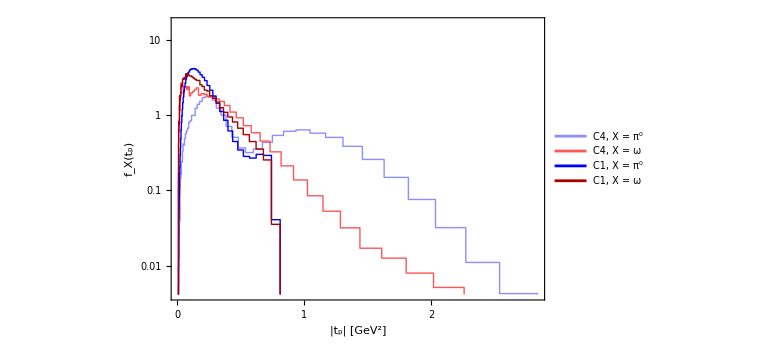
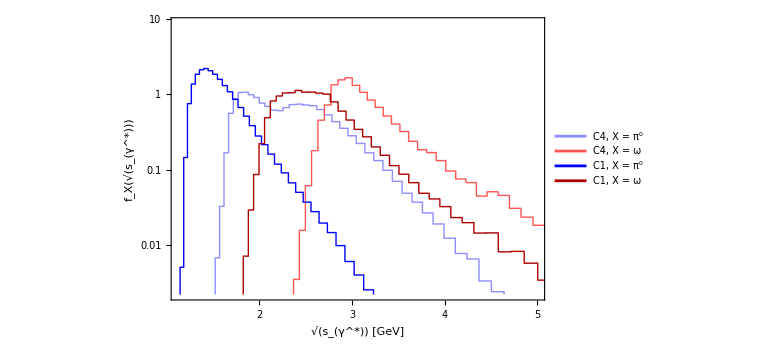

/Users/maksymovchynnikov/Library/CloudStorage/Dropbox/Science 2/HNL and scalar phenomenology/ALPs at EIC/release/plots/PDF-sgammap.pdf

```mathematica
pt1=With[{mes="π^0",set="100×10"},ListLogPlot[{pdfDataNoCuts[set,mes,"t_p"],pdfDataCuts[set,mes,"t_p"]},PlotRange->{All,{10^-6.,4}*Max[pdfDataNoCuts[set,mes,"t_p"][[All,2]]]},Joined->True,InterpolationOrder->0,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],FrameLabel->{"|t_p| [GeV^2]","PDF[t_p]"},ImageSize->Large,PlotLabel->Style[Row[{mes,", ",set}],20,FontFamily->"Palatino",Black],PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"No cuts","After cuts"}, {0.8,0.9}]]];
pt2=With[{mes="π^0",set="41×5"},ListLogPlot[{pdfDataNoCuts[set,mes,"√(s_(γ^*))"],pdfDataCuts[set,mes,"√(s_(γ^*))"]},PlotRange->{{Min[pdfDataNoCuts[set,mes,"√(s_(γ^*))"][[All,1]]],6},{10^-6.,4}*Max[{pdfDataNoCuts[set,mes,"√(s_(γ^*))"][[All,2]],pdfDataCuts[set,mes,"√(s_(γ^*))"][[All,2]]}]},Joined->True,InterpolationOrder->0,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],FrameLabel->{"√(s_(γ^*)) [GeV]","PDF[√(s_(γ^*))]"},ImageSize->Large,PlotLabel->Style[Row[{mes,", ",set}],20,FontFamily->"Palatino",Black],PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"No cuts","After cuts"}, {0.8,0.9}]]];
tabsToPlot=pdfDataCuts[#[[1]],#[[2]],"t_p"]&/@mesonsDatasetups;
legends=Row[{compactNameConf[#[[1]]],", X = ",#[[2]]}]&/@mesonsDatasetups;
{range1,range2}=(Flatten[tabsToPlot,1][[All,#]]//MinMax)&/@{1,2};
range2={10^-3,4}*range2[[2]];
pt1Paper=ListLogPlot[tabsToPlot,PlotRange->{range1,range2},Joined->True,InterpolationOrder->0,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotStyle->{{Thick,Lighter@Lighter@Blue},{Thick,Lighter@Red},{Thick,Blue},{Thick,Darker@Red}},FrameLabel->{"|t_p| [GeV^2]","f_X(t_p)"},ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@legends, {0.82,0.76}],FrameTicks->ticks];
Export[FileNameJoin[{dir["plots"],"PDF-tp.pdf"}],pt1Paper]
(*Subscript[s, γ^*p]*)
tabsToPlot=pdfDataCuts[#[[1]],#[[2]],"√(s_(γ^*))"]&/@mesonsDatasetups;
legends=Row[{compactNameConf[#[[1]]],", X = ",#[[2]]}]&/@mesonsDatasetups;
{range1,range2}=(Flatten[tabsToPlot,1][[All,#]]//MinMax)&/@{1,2};
range1={range1[[1]],Min[5.,range1[[2]]]};
range2={10^-3,4}*range2[[2]];
pt2Paper=ListLogPlot[tabsToPlot,PlotRange->{range1,range2},Joined->True,InterpolationOrder->0,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotStyle->{{Thick,Lighter@Lighter@Blue},{Thick,Lighter@Red},{Thick,Blue},{Thick,Darker@Red}},FrameLabel->{"√(s_(γ^*)) [GeV]","f_X(√(s_(γ^*)))"},ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@legends, {0.82,0.76}],FrameTicks->ticks];
Style[Row[{pt1Paper,pt2Paper}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{dir["plots"],"PDF-sgammap.pdf"}],pt2Paper]
```

#### Plots - Q^2

Imposing cuts

```mathematica
ResourceFunction["MonitorProgress"]@Do[
Block[{setup,mes,Ep,Ee,mX,Q2minFBD=0.9*10^-3.,Q2maxFBD=10.,ifFBD=True,ifMid=True,ηMid=4.,ηpprMin=4.5,ηXmin=-4.,ηXmax=4.},
{setup,mes}=f;
mX=MASS[mes];
{Ep,Ee}=energies[setup];
funcOwn[ptsKin_,weights_]:=cutFuncComp[ptsKin,weights,MASS[mes],0.5*Ep,0.9*Ep,ηpprMin,ηXmin,ηXmax,ifFBD,ifMid];
cuttedData[setup,mes]=BlockFinalAlt[mes,MASS[mes],fatest,Ep,Ee,mesonSample[setup,mes],funcOwn];
pdfDataCuts[setup,mes,"Q^2"]=pdf1Dmaker[cuttedData[setup,mes],indexFint1,50];
pdfDataNoCuts[setup,mes,"Q^2"]=pdf1Dmaker[mesonSample[setup,mes],indexFint1,50];
]
,{f,mesonsDatasetups}]
```

Plots

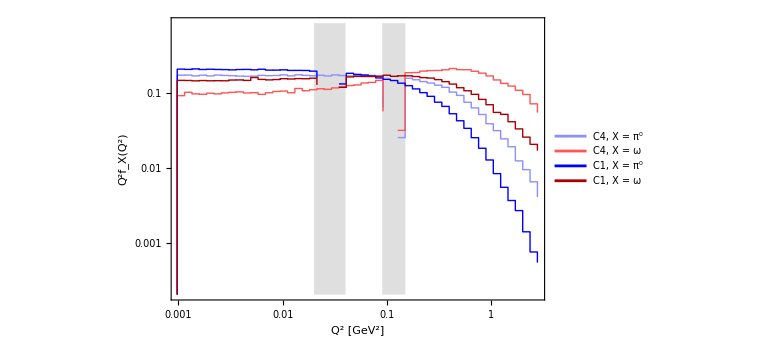

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\PDF-Q2.pdf

```mathematica
tabsToPlot=Table[{#[[1]],#[[2]]*#[[1]]}&/@pdfDataCuts[f[[1]],f[[2]],"Q^2"],{f,mesonsDatasetups}];
{range1,range2}=(Flatten[tabsToPlot,1][[All,#]]//MinMax)&/@{1,2};
range1={Max[10^-3.,range1[[1]]],Min[5.,range1[[2]]]};
range2={10^-3,4}*range2[[2]];
legends=Row[{compactNameConf[#[[1]]],", X = ",#[[2]]}]&/@mesonsDatasetups;
pt3Paper=ListLogLogPlot[tabsToPlot,PlotRange->{range1,range2},Joined->True,InterpolationOrder->0,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotStyle->{{Thick,Lighter@Lighter@Blue},{Thick,Lighter@Red},{Thick,Blue},{Thick,Darker@Red}},FrameLabel->{"Q^2 [GeV^2]","Q^2f_X(Q^2)"},ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],22,Black,FontFamily->"Palatino"]&/@legends,{0.16,0.24}],FrameTicks->ticksLogX,Prolog->{EdgeForm[None],FaceForm[Directive[Gray,Opacity[0.25]]],(*0.02<Q^2<0.04*)Rectangle[{Log[0.02],Log[range2[[1]]]},{Log[0.04],Log[range2[[2]]]}],(*0.09<Q^2<0.15<--change 0.15 if needed*)Rectangle[{Log[0.09],Log[range2[[1]]]},{Log[0.15],Log[range2[[2]]]}]}]
Export[FileNameJoin[{dir["plots"],"PDF-Q2.pdf"}],pt3Paper]
```

### Plots - Q^2 vs η_e' and Q^2 vs E_e'

#### Generating PDFs

```mathematica
{setup,pt}={"100×10","η"};
pdf2D1=pdf2Dmaker[mesonSample[setup,pt],indexFinEepr,indexFint1,30,30];//AbsoluteTiming
dataconv=Hold@Compile[{{data,_Real,1}},Module[{cos=data[[indexFincosθepr]]},
{1/2 Log[(1+cos)/(1-cos)],-data[[indexFint1]]}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleOwn[{indexFincosθepr,indexFint1}]//ReleaseHold;
checkIfCompiled[dataconv]
pdf2D2=With[{datTemp=dataconv[mesonSample[setup,pt]]},pdf2Dmaker[datTemp,1,2,30,30]];//AbsoluteTiming
```

{7.58086,Null}

{True,{}}

{2.57254,Null}

#### Plots

```mathematica
labelPlot=Row[{"E_p×E_e = ",energies[setup][[1]]//IntegerPart," GeV×",energies[setup][[2]]//IntegerPart," GeV, ",pt," meson"}];
labelEpilog=Row[{""}];
ptCorr1=plotDensity[pdf2D1,False,True,True,"E_e' [GeV]","Q^2 [GeV^2]",{0.16,0.3},labelEpilog,labelPlot];
ptCorr2=plotDensity[pdf2D2,False,True,True,"|η_e'|","Q^2 [GeV^2]",{0.16,0.3},labelEpilog,labelPlot];
Style[Row[{ptCorr1,ptCorr2}],ImageSizeMultipliers->{1,1}]
Export[FileNameJoin[{dir["plots"],"Correlation-Q2-Eepr.png"}],ptCorr1,ImageResolution->500];
Export[FileNameJoin[{dir["plots"],"Correlation-Q2-etaepr.png"}],ptCorr2,ImageResolution->500];
```

-Graphics--Graphics-

### Plots - η_e' vs E_e'

#### Defining the function imposing cuts

```mathematica
cutFuncComp=Hold@Compile[{{ptsKin,_Real,1},{weights,_Real},{ifFBD,True|False},{ifMid,True|False},{EALPmin,_Real},{EpprMin,_Real},{EpprMax,_Real},{etaPmin,_Real},{etaXmin,_Real},{etaXmax,_Real}},Module[{Eppr,EALP,Eepr,cppr,cX,cepr,s2,t1,t2,s1,(*robust eta from cos(theta):eta=0.5 Log((1+c)/(1-c))*)eps=1.*^-12,cClip,etaPpr,etaX,ϕSuppression=0.,ηepr=0.,pass=False,passFin=0,Q2FBDmin=10^-3.,ηeprFBDmax=-4.2,ηMidCut=4.},
{s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr,etaPpr,etaX}=ptsKin;
pass=((EALP>EALPmin)&&(EpprMin<Eppr<EpprMax)&&(etaPpr>etaPmin)&&etaXmin<etaX<etaXmax);
ηepr=1/2 Log[(1+cepr)/(1.-cepr)];
If[ifFBD,
pass=pass&&(Q2FBDmin<-t1)&&ηepr<ηeprFBDmax
];
If[ifMid,
pass=pass&&(Abs[ηepr]<ηMidCut);
];
passFin=Boole[pass];
{weights*passFin,s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr,etaPpr,etaX,ηepr}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleOwn[{Q2minEIC,Q2maxEIC}]//ReleaseHold;
checkIfCompiled[cutFuncComp]
```

{True,{}}

#### Imposing cuts and generating PDFs

```mathematica
{setup,mes}={"100×10","η"};
Block[{Ep,Ee,mX,ηpprMin=4.5,ηXmin=-4.,ηXmax=4.},
mX=MASS[mes];
{Ep,Ee}=energies[setup];
funcOwn[ptsKin_,weights_]:=cutFuncComp[ptsKin,weights,True,False,mX,0.5*Ep,0.9*Ep,ηpprMin,ηXmin,ηXmax];
cuttedDataFBD[setup,mes]=BlockFinalAlt[mes,mX,fatest,Ep,Ee,mesonSample[setup,mes],funcOwn];
pdfDataCuts[setup,mes,"FBD"]=pdf2Dmaker[cuttedDataFBD[setup,mes],indexFinEepr,-1,50,50];
funcOwn[ptsKin_,weights_]:=cutFuncComp[ptsKin,weights,False,True,mX,0.5*Ep,0.9*Ep,ηpprMin,ηXmin,ηXmax];
cuttedDataMid[setup,mes]=BlockFinalAlt[mes,mX,fatest,Ep,Ee,mesonSample[setup,mes],funcOwn];
pdfDataCuts[setup,mes,"Mid"]=pdf2Dmaker[cuttedDataMid[setup,mes],indexFinEepr,-1,50,50];
]
```

#### Plots

```mathematica
labelPlot=Row[{compactNameConf[setup],", ",mes," meson"}];
labelEpilog=Row[{""}];
ptCorr1=plotDensity[pdfDataCuts[setup,mes,"FBD"],False,False,True,"E_e' [GeV]","|η_e'|",{0.16,0.3},labelEpilog,labelPlot,{9.93,10.},Automatic,"f"];
ptCorr2=plotDensity[pdfDataCuts[setup,mes,"Mid"],False,False,True,"E_e' [GeV]","|η_e'|",{0.16,0.3},labelEpilog,labelPlot,{9.93,10.},Automatic,"f"];
Style[Row[{ptCorr1,ptCorr2}],ImageSizeMultipliers->{1,1}]
Export[FileNameJoin[{dir["plots"],"Correlation-etaepr-Eepr-FBD.png"}],ptCorr1,ImageResolution->500];
Export[FileNameJoin[{dir["plots"],"Correlation-etaepr-Epr-Mid.png"}],ptCorr2,ImageResolution->500];
```

-Graphics--Graphics-

## Plots - overall cross-sections for various EIC setups

### Defining the cut function

```mathematica
fractionηCutComp=Hold@Compile[{{ptsKin,_Real,1},{weights,_Real},{EALPmin,_Real},{EpprMin,_Real},{EpprMax,_Real},{etaPmin,_Real},{etaXmin,_Real},{etaXmax,_Real},{ifFBD,True|False},{ifMid,True|False}},Module[{Eppr,EALP,Eepr,cppr,cX,cepr,s2,t1,t2,s1,(*robust eta from cos(theta):eta=0.5 Log((1+c)/(1-c))*)eps=1.*^-12,cClip,etaPpr,etaX,pass=1.,ϕSuppression=0.,ηepr=0.,Q2minFBD=10^-3.,ηeprMaxFBD=-4.2,ηMidηCut=4.},
{s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr}=ptsKin;
cClip=cppr;
If[cClip>1.-eps,cClip=1.-eps];
If[cClip<-1.+eps,cClip=-1.+eps];
etaPpr=0.5*Log[(1.+cClip)/(1.-cClip)];
cClip=cX;
If[cClip>1.-eps,cClip=1.-eps];
If[cClip<-1.+eps,cClip=-1.+eps];
etaX=0.5*Log[(1.+cClip)/(1.-cClip)];
pass=Boole[(EALP>EALPmin)&&(EpprMin<Eppr<EpprMax)&&(etaPpr>etaPmin)&&etaXmin<etaX<etaXmax ];
ηepr=1/2. Log[(1+cepr)/(1-cepr)];
If[ifFBD,
pass=pass*Boole[Q2minFBD<-t1&&ηepr<ηeprMaxFBD];
];
If[ifMid,

pass=pass*Boole[Abs[ηepr]<ηMidηCut];
];
{weights*pass,s2,t1,t2,s1,Eppr,EALP,Eepr,cppr,cX,cepr,etaPpr,etaX}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleOwn[{}]//ReleaseHold;
checkIfCompiled[fractionηCutComp]
```

{True,{}}

#### Generating the data

```mathematica
econfigurations=Select[EnergiesConfigurations,!MemberQ[{"Baseline","Baseline-FBD-upgrade","Optimal","High-energy"},#]&];
{σListFBD,σListMidη}//ClearAll;
parts={"η","ω"};
ResourceFunction["MonitorProgress"]@Do[
σListFBD[pt]=σListMidη[pt]={};
ResourceFunction["MonitorProgress"]@Do[
Block[{Ee,Ep,NevTest=2*10^7,mX=MASS[pt],fa=1.},
{Ep,Ee}=energies[econf];
funcOwn1[data_,weights_]:=fractionηCutComp[data,weights,mX,0.5*Ep,0.9*Ep,4.5,-4.,4.,True,False];
σListFBD[pt]=Join[σListFBD[pt],{Join[{econf},BlockFinal[pt,mX,fa,Ep,Ee,NevTest,mX,1.,2.,3.,4.,5.,6.,7.,False,False,False,False,True,funcOwn1,False]]}];
funcOwn1[data_,weights_]:=fractionηCutComp[data,weights,mX,0.5*Ep,0.9*Ep,4.5,-4.,4.,False,True];
σListMidη[pt]=Join[σListMidη[pt],{Join[{econf},BlockFinal[pt,mX,fa,Ep,Ee,NevTest,mX,1.,2.,3.,4.,5.,6.,7.,False,False,False,False,True,funcOwn1,False]]}];
]
,{econf,econfigurations}]
,{pt,parts}]//AbsoluteTiming
```

{471.531,Null}

#### Plot

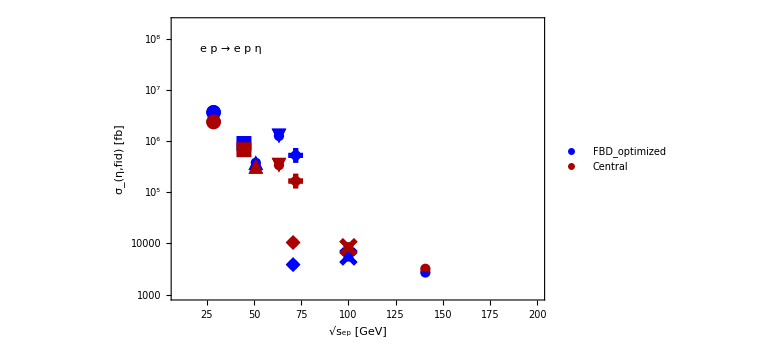
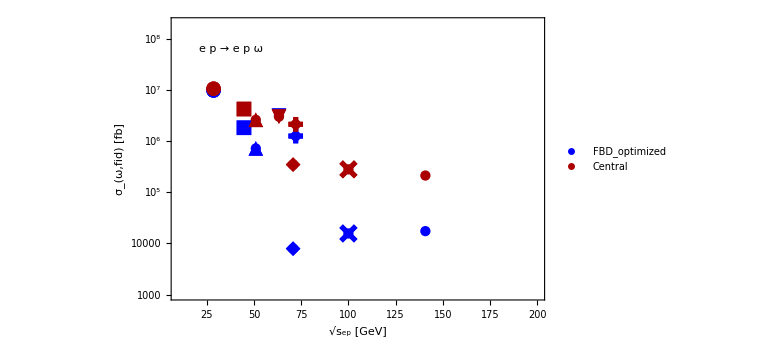

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\MPE-ECAL-vs-FBD-Eta.pdf

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\MPE-ECAL-vs-FBD-Omega.pdf

```mathematica
Do[
σListFBDfin[pt]={#[[1]],√(4*energies[#[[1]]][[1]]*energies[#[[1]]][[2]]),#[[2]],#[[3]]}&/@σListFBD[pt];
σListMidηFin[pt]={#[[1]],√(4*energies[#[[1]]][[1]]*energies[#[[1]]][[2]]),#[[2]],#[[3]]}&/@σListMidη[pt];
σListFBDtoPlot[pt]={#[[2]],btofb*#[[4]]}&/@σListFBDfin[pt];
σListMidηToPlot[pt]={#[[2]],btofb*#[[4]]}&/@σListMidηFin[pt];
,{pt,parts}]
legends=compactNameConf[#]&/@econfigurations;
markers={Graphics[{Disk[]},PlotRange->1],Graphics[{Rectangle[{-1,-1},{1,1}]},PlotRange->1],Graphics[{Polygon[{{0,1},{-1,-1},{1,-1}}]},PlotRange->1],Graphics[{Polygon[{{0,-1},{-1,1},{1,1}}]},PlotRange->1],Graphics[{Polygon[{{0,1},{-1,0},{0,-1},{1,0}}]},PlotRange->1],Graphics[{Thickness[.18],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]},PlotRange->1],Graphics[{Thickness[.18],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]},PlotRange->1],Graphics[{Thickness[.14],Circle[],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]},PlotRange->1]};
(*legend for marker shapes*)
cLegend=Framed[PointLegend[ConstantArray[Directive[Gray],8],legends,LegendMarkers->Thread[{markers,12}],LabelStyle->Directive[18,Black,FontFamily->"Palatino"],LegendLayout->"Column"(*,Spacings->{0.6,0.35}*)],Background->White,FrameStyle->Directive[Black,Thick],RoundingRadius->6,FrameMargins->8];
plotσFidSetup[pt_]:=Block[{basePlot},
epilog={Inset[Framed[Style[Row[{"e p → e p ",pt}],22,Black,FontFamily->"Palatino"],FrameStyle->Directive[Black,Thickness[0.9]],Background->White,FrameMargins->Medium],Scaled[{0.22,0.89}]]};
basePlot=ListLogPlot[{σListFBDtoPlot[pt],σListMidηToPlot[pt]},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],ImageSize->Large,PlotRange->{{10,200},{(*10^-12 btofb*)10^3,2*(*10^-8 btofb*)10^8}},FrameLabel->{"√s_ep [GeV]",Row[{Subscript["σ",pt<>",fid"]," [fb]"}]},PlotStyle->({Thickness[0.003],#}&/@{ Blue,Darker@Red}),PlotMarkers->None,FrameTicks->ticksXlinearWide,Epilog->epilog];
splitData=Join[List/@σListFBDtoPlot[pt],List/@σListMidηToPlot[pt]];
splitColors=Join[ConstantArray[Blue,Length[σListFBDtoPlot[pt]]],ConstantArray[Darker@Red,Length[σListMidηToPlot[pt]]]];
markerOverlay=ListLogPlot[splitData,PlotRange->{{20,150},All},PlotStyle->({Thickness[0.003],#}&/@splitColors),PlotMarkers->Thread[{markers,15}],PlotLegends->None,Axes->False,Frame->False];
ptleg=ListPlot[{Table[{x,x},{x,0.1,1,2}],Table[{x,x},{x,0.1,1,2}]},PlotStyle->Evaluate[{Thick,#,PointSize[0.01]}&/@DeleteDuplicates[splitColors]],PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"FBD_optimized","Central"},{0.14,0.13}]];
plotEnergies=Show[basePlot,markerOverlay,ptleg,Epilog->{Inset[cLegend,Scaled[{0.8,0.02}],{Left,Bottom}],Inset[Framed[Style[Row[{"e p → e p ",pt}],22,Black,FontFamily->"Palatino"],FrameStyle->Directive[Black,Thickness[0.9]],Background->White,FrameMargins->Medium],Scaled[{0.16,0.89}]]}];
plotEnergies
]
plotpt1=plotσFidSetup["η"];
plotpt2=plotσFidSetup["ω"];
Style[Row[{plotpt1,plotpt2}],ImageSizeMultipliers->{1,1}]
Export[FileNameJoin[{dir["plots"],"MPE-ECAL-vs-FBD-Eta.pdf"}],plotpt1]
Export[FileNameJoin[{dir["plots"],"MPE-ECAL-vs-FBD-Omega.pdf"}],plotpt2]
```

#### Plots - η_p' vs η_X

Generating PDFs

```mathematica
dataconv=Hold@Compile[{{data,_Real,1}},Module[{cos1=data[[indexFincosθppr]],cos2=data[[indexFincosθALP]]},
{1/2 Log[(1+cos1)/(1-cos1)],1/2 Log[(1+cos2)/(1-cos2)]}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleOwn[{indexFincosθALP,indexFincosθppr}]//ReleaseHold;
checkIfCompiled[dataconv]
quickSelector=Hold@Compile[{{data,_Real,2},{Epcut,_Real}},Select[data,#[[indexFinEppr]]<Epcut&],CompilationTarget->"C",RuntimeOptions->"Speed"]/.ruleOwn[{indexFinEppr}]//ReleaseHold;
checkIfCompiled[quickSelector]
particle="η";
setup1="275×18";
pdf2D1=With[{datTemp=quickSelector[mesonSample[setup1,particle],0.9*energies[setup1][[1]]]},pdf2Dmaker[dataconv[datTemp],1,2,25,25]];//AbsoluteTiming
setup2="41×5";
pdf2D2=With[{datTemp=quickSelector[mesonSample[setup2,particle],0.9*energies[setup2][[1]]]},pdf2Dmaker[dataconv[datTemp],1,2,25,25]];//AbsoluteTiming
```

{True,{}}

{True,{}}

{19.3882,Null}

{1.54845,Null}

Plot

```mathematica
{labelPlot1,labelPlot2}=Row[{"E_p×E_e = ",energies[#][[1]]//IntegerPart," GeV×",energies[#][[2]]//IntegerPart," GeV, ",particle," meson"}]&/@{setup1,setup2};
labelEpilog1=labelEpilog2=Row[{""}];
ptCorr1=plotDensity[pdf2D1,False,False,True,"η_p'","η_X",{0.86,0.3},labelEpilog1,labelPlot1]
ptCorr2=plotDensity[pdf2D2,False,False,True,"η_p'","η_X",{0.86,0.3},labelEpilog2,labelPlot2]
Export[FileNameJoin[{dir["plots"],"Correlation-etaX-etapPr-high-energy.png"}],ptCorr1,ImageResolution->500];
Export[FileNameJoin[{dir["plots"],"Correlation-etaX-etapPr-low-energy.png"}],ptCorr2,ImageResolution->500];
```

-Graphics-

-Graphics-